# Logistic regression

### Sigmoid function

```mathematica
Sigmoid[z_]:=1/(1+Exp[-z]);
```

```mathematica
{#,N@Sigmoid[#]}&/@Range[-5,5]//TableForm
```

-5 | 0.00669285
-4 | 0.0179862
-3 | 0.0474259
-2 | 0.119203
-1 | 0.268941
0 | 0.5
1 | 0.731059
2 | 0.880797
3 | 0.952574
4 | 0.982014
5 | 0.993307

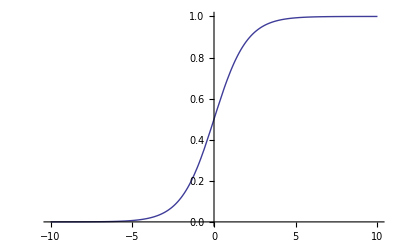

```mathematica
Plot[Sigmoid[x],{x,-10,10}]
```

```mathematica
range=5;
```

### Example data

There are two data files in CSV format.

```mathematica
$dataFile1=ToFileName[{NotebookDirectory[]},"ex2data1.txt"];
$dataFile2=ToFileName[{NotebookDirectory[]},"ex2data2.txt"];
```

The data files happen to be CSV file, import as so.

```mathematica
data1=Import[$dataFile1,"CSV"];
data2=Import[$dataFile2,"CSV"];
```

```mathematica
ex1=data1[[All,{1,2}]];
```

```mathematica
X1=Prepend[#,1]&/@ex1;
y1=data1[[All,3]];
```

```mathematica
X1//RandomChoice
```

{1,67.9469,46.6786}

Visualize the feature matrix X:

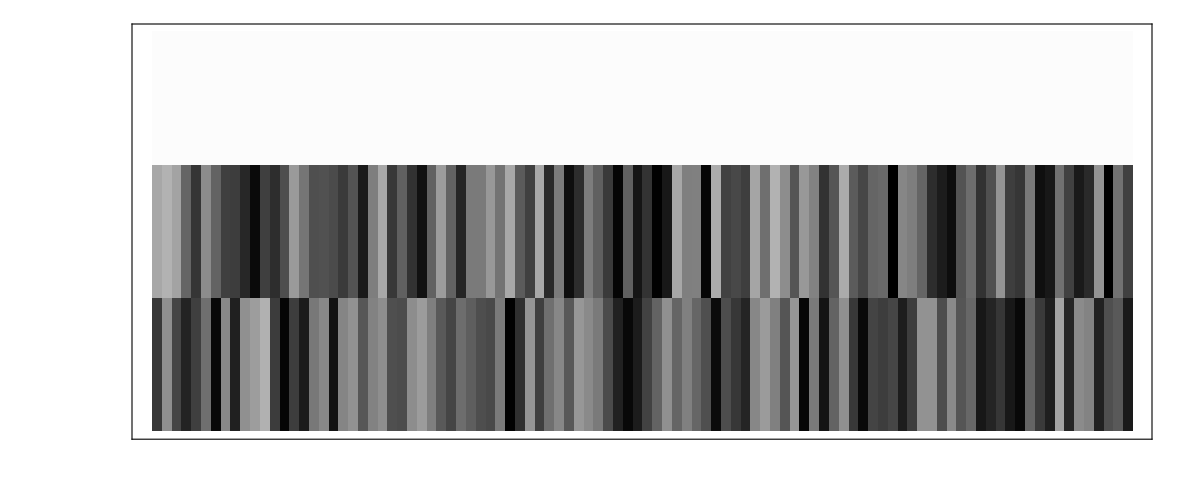

```mathematica
X1//Transpose//ArrayPlot[#,ImageSize-> 1200,Frame-> True,PlotRangePadding-> None]&
```

Find the data points in the “admitted” and “not admitted” types:

```mathematica
ex1Admitted=Cases[data1,{x_,y_,1}:> {x,y}];
ex1NotAdmitted=Cases[data1,{x_,y_,0}:> {x,y}];
```

Plot it in the parameter space to get an idea of distribution:

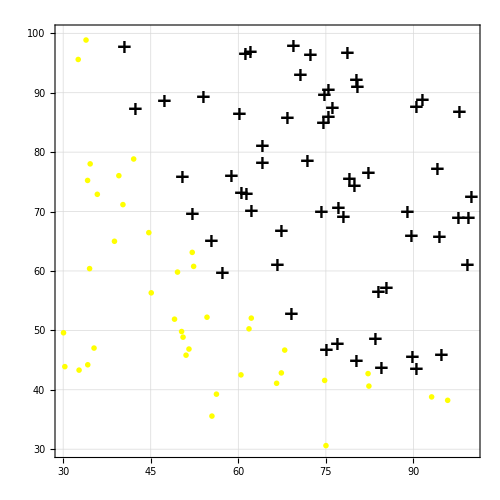

```mathematica
ListPlot[{ex1Admitted,ex1NotAdmitted},
ImageSize-> 500,AspectRatio-> 1,
Frame-> True,GridLines-> Automatic,PlotRange-> {{30,100},{30,100}},
PlotStyle-> {Directive[Black,PointSize[Large]],Directive[Yellow,PointSize[Large]]},
PlotMarkers-> {Style["+",FontSize-> 20,FontWeight-> Bold],Graphics[{EdgeForm[Thick],Yellow,Disk[{0,0},Scaled[0.02]]}]}
]
```

```mathematica
ex2=data2[[All,{1,2}]];
```

```mathematica
X2=Prepend[#,1]&/@ex2;
y2=data2[[All,3]];
```

```mathematica
X2//RandomChoice
```

{1,-0.16187,0.8019}

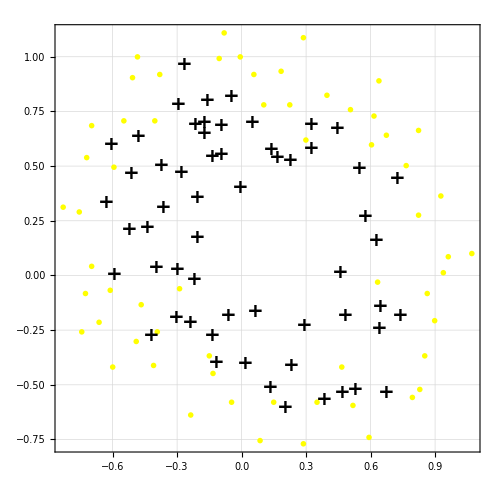

```mathematica
ex2Admitted=Cases[data2,{x_,y_,1}:> {x,y}];
ex2NotAdmitted=Cases[data2,{x_,y_,0}:> {x,y}];
ListPlot[{ex2Admitted,ex2NotAdmitted},
ImageSize-> 500,AspectRatio-> Automatic,
Frame-> True,GridLines-> Automatic,PlotRange-> Automatic,
PlotStyle-> {Directive[Black,PointSize[Large]],Directive[Yellow,PointSize[Large]]},
PlotMarkers-> {Style["+",FontSize-> 20,FontWeight-> Bold],Graphics[{EdgeForm[Thick],Yellow,Disk[{0,0},Scaled[0.02]]}]}
]
```

### Cost function

Hypothesis function h as a function of fitting parameter and feature matrix:

```mathematica
h[θ_,X_]:=Sigmoid[X.θ];
```

Cost function J as a function of fitting parameter and the example data set including the feature matrix X and the observed dependent variable y:

```mathematica
J[θ_,X_,y_]:=-1/Length[y](y.Log[h[θ,X]]+(1-y).Log[1-h[θ,X]])
```

Define the fitting parameter in to the vector with right dimension:

```mathematica
Clear[θ]
θ=Table[Symbol["θ"<>ToString[j]],{j,0,Length[X1[[1]]]-1}]
```

{θ0,θ1,θ2}

Cost function at {0, 0, 0}

```mathematica
J[{0,0,0},X1,y1]
```

0.693147

### Find θ to minimize cost function

```mathematica
NMinimize[J[{θ0,θ1,θ2},X1,y1],{θ0,θ1,θ2}]
```

NMinimize::nnum: The function value Indeterminate is not a number at {θ0, θ1, θ2} = {0.673558, 0.659492, 0.0861047}.

NMinimize[1/100 (-Log[1/(1+ⅇ^(-θ0-69.3646 θ1-97.7187 θ2))]-Log[1/(1+ⅇ^(-θ0-40.4576 θ1-97.5352 θ2))]-Log[1/(1+ⅇ^(-θ0-62.0731 θ1-96.7688 θ2))]-Log[1/(1+ⅇ^(-θ0-78.6354 θ1-96.6474 θ2))]-Log[1/(1+ⅇ^(-θ0-61.1067 θ1-96.5114 θ2))]-Log[1/(1+ⅇ^(-θ0-72.3465 θ1-96.2276 θ2))]-Log[1/(1+ⅇ^(-θ0-70.6615 θ1-92.9271 θ2))]-Log[1/(1+ⅇ^(-θ0-80.2796 θ1-92.1161 θ2))]-Log[1/(1+ⅇ^(-θ0-80.3668 θ1-90.9601 θ2))]-Log[1/(1+ⅇ^(-θ0-75.4777 θ1-90.4245 θ2))]-Log[1/(1+ⅇ^(-θ0-74.7759 θ1-89.5298 θ2))]-Log[1/(1+ⅇ^(-θ0-53.9711 θ1-89.2074 θ2))]-Log[1/(1+ⅇ^(-θ0-91.565 θ1-88.6963 θ2))]-Log[1/(1+ⅇ^(-θ0-47.2643 θ1-88.4759 θ2))]-Log[1/(1+ⅇ^(-θ0-90.4486 θ1-87.5088 θ2))]-Log[1/(1+ⅇ^(-θ0-76.0988 θ1-87.4206 θ2))]-Log[1/(1+ⅇ^(-θ0-42.2617 θ1-87.1039 θ2))]-Log[1/(1+ⅇ^(-θ0-97.7716 θ1-86.7278 θ2))]-Log[1/(1+ⅇ^(-θ0-60.1826 θ1-86.3086 θ2))]-Log[1/(1+ⅇ^(-θ0-75.3956 θ1-85.7599 θ2))]-Log[1/(1+ⅇ^(-θ0-68.4685 θ1-85.5943 θ2))]-Log[1/(1+ⅇ^(-θ0-74.4927 θ1-84.8451 θ2))]-Log[1/(1+ⅇ^(-θ0-64.177 θ1-80.9081 θ2))]-Log[1/(1+ⅇ^(-θ0-71.7965 θ1-78.4536 θ2))]-Log[1/(1+ⅇ^(-θ0-64.0393 θ1-78.0317 θ2))]-Log[1/(1+ⅇ^(-θ0-94.0943 θ1-77.1591 θ2))]-Log[1/(1+ⅇ^(-θ0-82.3071 θ1-76.482 θ2))]-Log[1/(1+ⅇ^(-θ0-58.841 θ1-75.8584 θ2))]-Log[1/(1+ⅇ^(-θ0-50.4582 θ1-75.8099 θ2))]-Log[1/(1+ⅇ^(-θ0-79.0327 θ1-75.3444 θ2))]-Log[1/(1+ⅇ^(-θ0-79.9448 θ1-74.1631 θ2))]-Log[1/(1+ⅇ^(-θ0-60.4579 θ1-73.095 θ2))]-Log[1/(1+ⅇ^(-θ0-61.3793 θ1-72.8079 θ2))]-Log[1/(1+ⅇ^(-θ0-99.8279 θ1-72.3693 θ2))]-Log[1/(1+ⅇ^(-θ0-77.193 θ1-70.4582 θ2))]-Log[1/(1+ⅇ^(-θ0-62.271 θ1-69.9545 θ2))]-Log[1/(1+ⅇ^(-θ0-74.2487 θ1-69.8246 θ2))]-Log[1/(1+ⅇ^(-θ0-88.9139 θ1-69.8038 θ2))]-Log[1/(1+ⅇ^(-θ0-52.0454 θ1-69.4329 θ2))]-Log[1/(1+ⅇ^(-θ0-77.9241 θ1-68.9724 θ2))]-Log[1/(1+ⅇ^(-θ0-97.6456 θ1-68.8616 θ2))]-Log[1/(1+ⅇ^(-θ0-99.315 θ1-68.7754 θ2))]-Log[1/(1+ⅇ^(-θ0-67.3193 θ1-66.5894 θ2))]-Log[1/(1+ⅇ^(-θ0-89.6768 θ1-65.7994 θ2))]-Log[1/(1+ⅇ^(-θ0-94.4434 θ1-65.5689 θ2))]-Log[1/(1+ⅇ^(-θ0-55.34 θ1-64.9319 θ2))]-Log[1/(1+ⅇ^(-θ0-99.2725 θ1-60.999 θ2))]-Log[1/(1+ⅇ^(-θ0-66.7467 θ1-60.9914 θ2))]-Log[1/(1+ⅇ^(-θ0-57.2387 θ1-59.5143 θ2))]-Log[1/(1+ⅇ^(-θ0-85.4045 θ1-57.052 θ2))]-Log[1/(1+ⅇ^(-θ0-83.9024 θ1-56.308 θ2))]-Log[1/(1+ⅇ^(-θ0-69.0701 θ1-52.7405 θ2))]-Log[1/(1+ⅇ^(-θ0-83.4892 θ1-48.3803 θ2))]-Log[1/(1+ⅇ^(-θ0-76.9788 θ1-47.576 θ2))]-Log[1/(1+ⅇ^(-θ0-75.0247 θ1-46.554 θ2))]-Log[1/(1+ⅇ^(-θ0-94.8345 θ1-45.6943 θ2))]-Log[1/(1+ⅇ^(-θ0-89.8458 θ1-45.3583 θ2))]-Log[1/(1+ⅇ^(-θ0-80.1902 θ1-44.8216 θ2))]-Log[1/(1+ⅇ^(-θ0-84.4328 θ1-43.5334 θ2))]-Log[1/(1+ⅇ^(-θ0-90.5467 θ1-43.3906 θ2))]-Log[1-1/(1+ⅇ^(-θ0-33.9155 θ1-98.8694 θ2))]-Log[1-1/(1+ⅇ^(-θ0-32.5772 θ1-95.5985 θ2))]-Log[1-1/(1+ⅇ^(-θ0-42.0755 θ1-78.8448 θ2))]-Log[1-1/(1+ⅇ^(-θ0-34.6237 θ1-78.0247 θ2))]-Log[1-1/(1+ⅇ^(-θ0-39.5383 θ1-76.0368 θ2))]-Log[1-1/(1+ⅇ^(-θ0-34.1836 θ1-75.2377 θ2))]-Log[1-1/(1+ⅇ^(-θ0-35.8474 θ1-72.9022 θ2))]-Log[1-1/(1+ⅇ^(-θ0-40.2369 θ1-71.1677 θ2))]-Log[1-1/(1+ⅇ^(-θ0-44.6683 θ1-66.4501 θ2))]-Log[1-1/(1+ⅇ^(-θ0-38.7858 θ1-64.9957 θ2))]-Log[1-1/(1+ⅇ^(-θ0-52.108 θ1-63.1276 θ2))]-Log[1-1/(1+ⅇ^(-θ0-52.348 θ1-60.7695 θ2))]-Log[1-1/(1+ⅇ^(-θ0-34.5245 θ1-60.3963 θ2))]-Log[1-1/(1+ⅇ^(-θ0-49.5867 θ1-59.809 θ2))]-Log[1-1/(1+ⅇ^(-θ0-45.0833 θ1-56.3164 θ2))]-Log[1-1/(1+ⅇ^(-θ0-54.6351 θ1-52.2139 θ2))]-Log[1-1/(1+ⅇ^(-θ0-62.2227 θ1-52.061 θ2))]-Log[1-1/(1+ⅇ^(-θ0-49.0726 θ1-51.8832 θ2))]-Log[1-1/(1+ⅇ^(-θ0-61.8302 θ1-50.2561 θ2))]-Log[1-1/(1+ⅇ^(-θ0-50.2865 θ1-49.8045 θ2))]-Log[1-1/(1+ⅇ^(-θ0-30.0588 θ1-49.593 θ2))]-Log[1-1/(1+ⅇ^(-θ0-50.5348 θ1-48.8558 θ2))]-Log[1-1/(1+ⅇ^(-θ0-35.2861 θ1-47.0205 θ2))]-Log[1-1/(1+ⅇ^(-θ0-51.5477 θ1-46.8563 θ2))]-Log[1-1/(1+ⅇ^(-θ0-67.9469 θ1-46.6786 θ2))]-Log[1-1/(1+ⅇ^(-θ0-51.0478 θ1-45.8227 θ2))]-Log[1-1/(1+ⅇ^(-θ0-34.2121 θ1-44.2095 θ2))]-Log[1-1/(1+ⅇ^(-θ0-30.2867 θ1-43.895 θ2))]-Log[1-1/(1+ⅇ^(-θ0-32.7228 θ1-43.3072 θ2))]-Log[1-1/(1+ⅇ^(-θ0-67.372 θ1-42.8384 θ2))]-Log[1-1/(1+ⅇ^(-θ0-82.2267 θ1-42.7199 θ2))]-Log[1-1/(1+ⅇ^(-θ0-60.4556 θ1-42.5084 θ2))]-Log[1-1/(1+ⅇ^(-θ0-74.7893 θ1-41.5734 θ2))]-Log[1-1/(1+ⅇ^(-θ0-66.5609 θ1-41.0921 θ2))]-Log[1-1/(1+ⅇ^(-θ0-82.3688 θ1-40.6183 θ2))]-Log[1-1/(1+ⅇ^(-θ0-56.2538 θ1-39.2615 θ2))]-Log[1-1/(1+ⅇ^(-θ0-93.1144 θ1-38.8007 θ2))]-Log[1-1/(1+ⅇ^(-θ0-95.8616 θ1-38.2253 θ2))]-Log[1-1/(1+ⅇ^(-θ0-55.4822 θ1-35.5707 θ2))]-Log[1-1/(1+ⅇ^(-θ0-75.0137 θ1-30.6033 θ2))]),{θ0,θ1,θ2}]

```mathematica
FindMinimum[J[{θ0,θ1,θ2},X1,y1],{θ0,0},{θ1,0},{θ2,0}]
```

FindMinimum::nrnum: The function value Indeterminate is not a real number at {θ0, θ1, θ2} = {0.00303682, 0.364698, 0.342032}.

{0.693147,{θ0→0.,θ1→0.,θ2→0.}}

#### this is the expected result

```mathematica
θSol={-24.932998,0.204408,0.199618}
```

{-24.933,0.204408,0.199618}

```mathematica
J[θSol,X1,y1]
```

0.203506